## Nomenclature

1=F=1,m_F=0,0ℏk
2=F=2,m_F=0,0ℏk
3=F=1,m_F=0,2ℏk

Spin operators (J_(x,y,z))^ij is defined as the operator J_(x,y,z) between state i and j

### Operator for 12 (microwave rotation)

RotEq mean a rotation along ax axis ϕ on the equator by θ
ϕ=0 means rotate along x-axis, ϕ=π/2 means rotate along y-axis

```mathematica
sx=1/2{{0,1},{1,0}};
sy=1/2{{0,-I},{I,0}};
sz=1/2{{1,0},{0,-1}};
s0={{1}};
```

```mathematica
Rot[ϕ_,θ_]:=MatrixExp[-ⅈ θ (Cos[ϕ] sx+Sin[ϕ]sy)]
v0={0,0};
Rotz[θ_]:=MatrixExp[-ⅈ θ sz]
```

```mathematica
v01={0,0,1};
RotEq12[ϕ_,θ_]:=Insert[Insert[Rot[ϕ,θ]//Transpose,v0,3]//Transpose,v01,3]
Rotz12[θ_]:=Insert[Insert[Rotz[θ]//Transpose,v0,3]//Transpose,v01,3]
```

### Operator for 23 (Raman rotation)

```mathematica
v02={1,0,0};
RotEq23[ϕ_,θ_]:=Insert[Insert[Rot[ϕ,θ]//Transpose,v0,1]//Transpose,v02,1]
Rotz23[θ_]:=Insert[Insert[Rotz[θ]//Transpose,v0,1]//Transpose,v02,1]
```

```mathematica
RotEq13[ϕ,θ]//MatrixForm
```

(1/2 ⅇ^(-(ⅈ θ)/2)+1/2 ⅇ^((ⅈ θ)/2) | 0 | -1/2 ⅇ^(-(ⅈ θ)/2) (-Cos[ϕ]+ⅈ Sin[ϕ])+1/2 ⅇ^((ⅈ θ)/2) (-Cos[ϕ]+ⅈ Sin[ϕ])
0 | 1 | 0
-1/2 ⅇ^(-(ⅈ θ)/2) (-Cos[ϕ]-ⅈ Sin[ϕ])+1/2 ⅇ^((ⅈ θ)/2) (-Cos[ϕ]-ⅈ Sin[ϕ]) | 0 | 1/2 ⅇ^(-(ⅈ θ)/2)+1/2 ⅇ^((ⅈ θ)/2))

### Operator for 13 (Bragg rotation)

```mathematica
v03={0,1,0};
RotEq13[ϕ_,θ_]:=Insert[Insert[Rot[ϕ,θ]//Transpose,v0,2]//Transpose,v03,2]
Rotz13[θ_]:=Insert[Insert[Rotz[θ]//Transpose,v0,2]//Transpose,v03,2]
```

### Microwave Ramsey interference

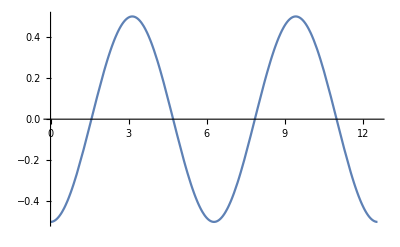

```mathematica
ψini=({{1}, {0}, {0}});
ψf=RotEq12[ϕ,π/2].RotEq12[0,π/2].ψini;
Plot[Transpose[Conjugate[ψf]].Sz12.ψf,{ϕ,0,4π}]
```

```mathematica
RotEq23[0,π]
```

{{1,0,0},{0,0,-ⅈ},{0,-ⅈ,0}}

```mathematica
RotEq12[0,π/2].ψini
```

{{1/(√2)},{-ⅈ/(√2)},{0}}

```mathematica
RotEq13[0,π/2].RotEq13[0,π].RotEq23[0,π].RotEq12[0,π/2].ψini
```

{{-1/2+ⅈ/2},{0},{1/2-ⅈ/2}}

```mathematica
tSz = {{1,0,0},{0,0,0},{0,0,-1}}/2;
```

### Hybrid interferometer

pi/2|_uwave→ pi|_Raman→ Tevol→ pi|_Bragg→ Tevol→ pi/2|_Bragg

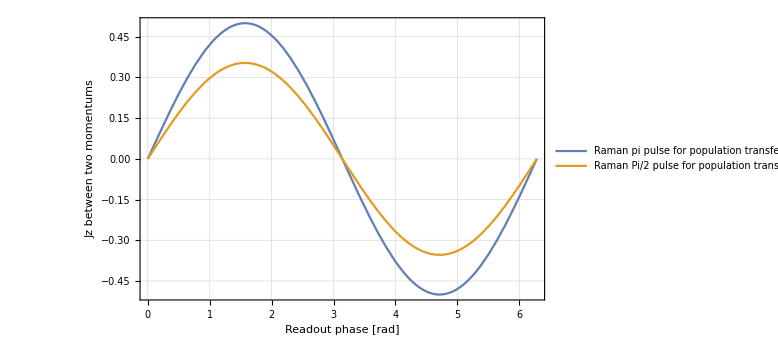

```mathematica
ψini=({{1}, {0}, {0}});
ψf=RotEq13[ϕ,π/2].RotEq13[0,π].RotEq23[0,π].RotEq12[0,π/2].ψini;
ψf1=RotEq13[ϕ,π/2].RotEq13[0,π].RotEq23[0,π/2].RotEq12[0,π/2].ψini;

Plot[
{Transpose[Conjugate[ψf]].tSz.ψf,Transpose[Conjugate[ψf1]].tSz.ψf1},
{ϕ,0,2π},
ImageSize->Large,
PlotLegends->{"Raman pi pulse for population transfer","Raman Pi/2 pulse for population transfer"},
Frame->True,
FrameLabel->{"Readout phase [rad]","Jz between two momentums"},
GridLines->Automatic,
LabelStyle->15]
```